# Grammar-based genetic programming

## Grammar definition and parsing

```mathematica
GrammarPrettifyRule[rule_]:=Style[rule["From"],Bold]->ReplaceAll[rule["To"],{NonTerm[arg_]:>Style[arg,Bold],Term[arg_]:>Style[arg,Italic]}];
GrammarPrettify[grammar_]:=Column[Map[GrammarPrettifyRule,grammar]];
grammar = {
<|"From"->"cond","To"->{Term["logicOp"],NonTerm["cond"],NonTerm["cond"]},
"Value"->Term["logicOp"]["Value"][NonTerm["cond"]["Value"],NonTerm["cond"]["Value"]]|>,
<|"From"->"cond","To"->{Term["not"],NonTerm["cond"]},
"Value"->Not[NonTerm["cond"]["Value"]]|>,
<|"From"->"cond","To"->{Term["numOp"],NonTerm["numQuant"],NonTerm["numQuant"]},
"Value"->Term["numOp"]["Value"][NonTerm["numQuant"]["Value"],NonTerm["numQuant"]["Value"]]|>,
<|"From"->"numQuant","To"->{Term["factor"],NonTerm["expression"]},
"Value"->Times[Term["factor"]["Value"],NonTerm["expression"]["Value"]]|>,
<|"From"->"numQuant","To"->{NonTerm["expression"]},
"Value"->NonTerm["expression"]["Value"]|>,
<|"From"->"expression","To"->{Term["techInd"],Term["observable"],Term["window"]},
"Value"->Term["techInd"]["Value"][Term["observable"]["Value"],Term["window"]["Value"]]|>,
<|"From"->"expression","To"->{Term["lag"],Term["observable"]},
"Value"->Prev[Term["observable"]["Value"],Term["lag"]["Value"]]|>,
<|"From"->"expression","To"->{Term["observable"]},
"Value"->Term["observable"]["Value"]|>
};
terminalSet = {
Term["logicOp","And"],Term["logicOp","Or"],Term["logicOp","Xor"],
Term["numOp","Greater"],Term["numOp","GreaterEqual"],Term["numOp","Less"],Term["numOp","LessEqual"],
Term["observable","Open"],Term["observable","Low"],Term["observable","High"],Term["observable","Close"],
Term["lag","1"],Term["lag","2"],Term["lag","3"],Term["lag","4"],Term["lag","5"],
Term["window","10"],Term["window","20"],Term["window","30"],Term["window","40"],Term["window","50"],
Term["factor","0.7"],Term["factor","0.9"],Term["factor","1.1"],Term["factor","1.3"]
};
```

```mathematica
GreaterEqual
```

```mathematica
Cases[labels1[[All,2]],_Term]
```

{Term[logicOp,And],Term[numOp,Greater],Term[observable,High],Term[lag,3],Term[observable,Low],Term[numOp,Less],Term[observable,Open],Term[observable,Close]}

```mathematica
GrammarPrettify[grammar]
```

cond→{logicOp,cond,cond}
cond→{not,cond}
cond→{numOp,numQuant,numQuant}
numQuant→{factor,expression}
numQuant→{expression}
expression→{techInd,observable,window}
expression→{lag,observable}
expression→{observable}

```mathematica
GrammarGraph[grammar_]:=Block[{graphData,allSymbols,colorStyle},
graphData = DeleteDuplicates[Flatten[Map[Thread,Map[(NonTerm[#["From"]]->#["To"])&,grammar]]]];
allSymbols = DeleteDuplicates[Flatten[Map[{NonTerm[#["From"]],#["To"]}&,grammar]]];
colorStyle = Join[Thread[Cases[allSymbols,_NonTerm]->Blue],Thread[Cases[allSymbols,_Term]->Red]];

Graph[graphData,VertexLabels->"Name",VertexStyle->colorStyle,ImageSize->800]
];
```

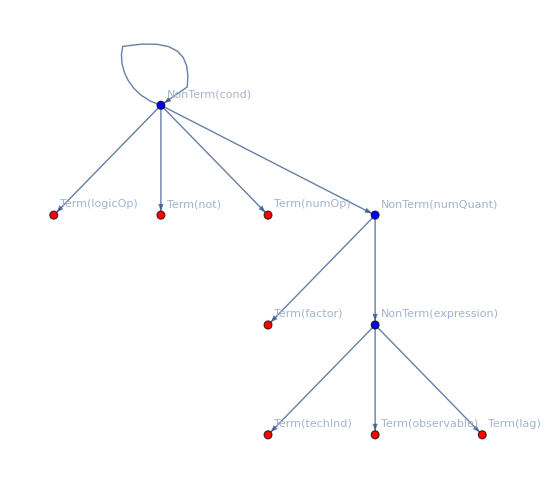

```mathematica
GrammarGraph[grammar]
```

```mathematica
GetComponents[expr_/;Depth[expr]<3]:={expr};
GetComponents[expr_/;Depth[expr]==3]:=Prepend[Level[expr,{1}],Head[expr]];
ExprFromComponents[components_ /;Length[components]≤1]:=First[components];
ExprFromComponents[components_ /;Length[components]>1]:=Block[{head,rest},
{head,rest} = {First[components],Rest[components]};
Apply[head,rest]
];

Synthesize[exprComponents_,synthValues_]:=Block[{positions,lastPos,tmpSynthValues = synthValues,tmpExprComponents = exprComponents},
Do[
positions = Position[tmpSynthValues[[All,1]],tmpExprComponents[[i]]];
If[positions≠ {},
lastPos = First@Last@positions;
tmpExprComponents[[i]] = Replace[tmpExprComponents[[i]],Part[tmpSynthValues,lastPos]];
tmpSynthValues = Delete[tmpSynthValues,lastPos];
];
,{i,1,Length[tmpExprComponents]}
];
ExprFromComponents@tmpExprComponents
];

MatchPositions[expr_,synthesizations_]:=Block[{pos,newSynth,recursive},
pos = FirstPosition[synthesizations,First[expr]];
If[pos =!=Missing["NotFound"],
newSynth = ReplacePart[synthesizations,First[pos]->Found],
newSynth = synthesizations;
pos = {};
];
recursive = If[Rest[expr]≠{},MatchPositions[Rest[expr],newSynth],{}];
Transpose@{Flatten@Join[pos,recursive]}
];
```

```mathematica
GetValue[treeSymbol_,grammar_]:=ReplaceAll[treeSymbol,NonTerm[_,rule_]:>grammar[[rule]]["Value"]];
SynthesizeNonTerm[treeSymbol_,grammar_,synthesizations_]:=Block[{val,eval,matchPos,newSynth,newSynthLabel},
val = GetValue[treeSymbol,grammar];
matchPos = MatchPositions[GetComponents[val],synthesizations[[All,1]]];
eval = Synthesize[GetComponents[val],Extract[synthesizations,matchPos]];
newSynth = Delete[synthesizations,matchPos];
newSynthLabel = ReplaceAll[treeSymbol,NonTerm[x_,_]:>NonTerm[x]["Value"]];

Prepend[newSynth,newSynthLabel->eval]
];

SynthesizeTerm[treeSymbol_,synthesizations_]:=Block[{eval,new},
(* Label the value of a Terminal *)
If[Length[treeSymbol]==2,
Prepend[synthesizations, ReplaceAll[treeSymbol,Term[termName_,value_]:>(Term[termName]["Value"]->value)]],
synthesizations
]
];
```

```mathematica
SynthesizeTree[graph_,labels_,grammar_]:=Block[{depthFirstScan,labeledDFS,symbolType,synthesized},
(* Walk the parse tree in post order *)
depthFirstScan = First@Last@Reap[
DepthFirstScan[graph,1,{"PostvisitVertex"->(Sow[#]&)}]
];
labeledDFS = depthFirstScan /.labels;

(* Synthesize in the order of the depthfirstscan *)
synthesized={};
Do[
symbolType = Head[s];
If[symbolType === Term,synthesized = SynthesizeTerm[s,synthesized]];
If[symbolType === NonTerm,synthesized = SynthesizeNonTerm[s,grammar,synthesized]];
,
{s,labeledDFS}
];

ToExpression@ToString@Return[synthesized[[1,-1]]];
];
```

```mathematica
edgeList1 = {1->2,1->3,1->4,3->5,3->6,3->7,6->8,8->9,7->10,10->11,10->12,4->13,4->14,4->15,14->16,16->17,15->18,18->19};
labels1 = {1->NonTerm["cond",1],2->Term["logicOp","And"],3->NonTerm["cond",3],4->NonTerm["cond",3],5->Term["numOp","Greater"] ,6->NonTerm["numQuant",5] ,7->NonTerm["numQuant",5] ,8->NonTerm["expression",8] ,9->Term["observable","High"] ,10->NonTerm["expression",7] ,11->Term["lag","3"] ,12->Term["observable","Low"] ,13->Term["numOp","Less"] ,14->NonTerm["numQuant",5] ,15->NonTerm["numQuant",5] ,16->NonTerm["expression",8] ,17->Term["observable","Open"] ,18-> NonTerm["expression",8],19-> Term["observable","Close"]};
```

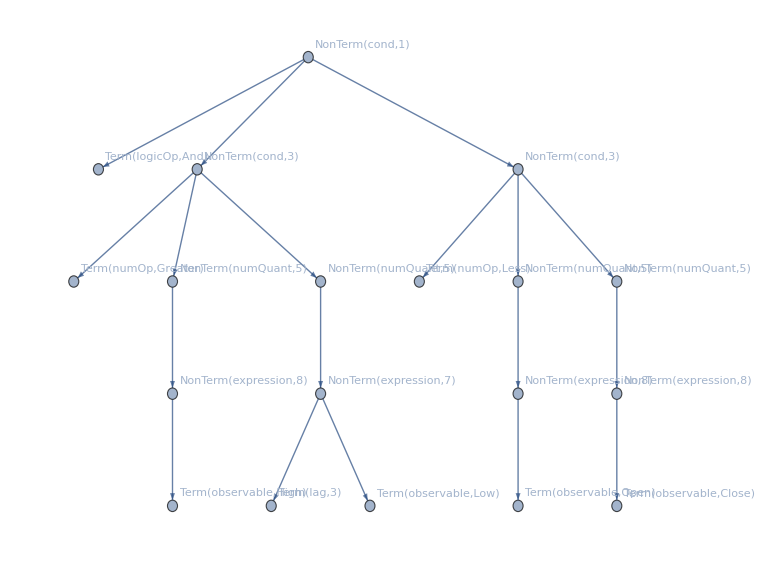

```mathematica
g1 = Graph[edgeList1,VertexLabels->labels1]
```

```mathematica
SynthesizeTree[g1,labels1,grammar] // FullForm
```

And[Greater[High,Prev[Low,3]],Less[Open,Close]]

```mathematica
edgeList2 = {1->2,1->3,1->4,3->5,3->6,3->7,6->8,6->9,9->10,9->11,9->12,7->13,13->14,13->15,13->16,4->17,4->18,4->19,18->20,20->21,20->22,19->23,23->24};
labels2 = {1->NonTerm["cond",1],2->Term["logicOp","Or"],3->NonTerm["cond",3],4->NonTerm["cond",3],5-> Term["numOp","Less"],6->NonTerm["numQuant",4] ,7-> NonTerm["numQuant",5],8->Term["factor","1.05"] ,9->NonTerm["expression",6] ,10-> Term["techInd","SMA"],11-> Term["observable","Close"],12->Term["window","20"] ,13->NonTerm["expression",6] ,14->Term["techInd","SMA"] ,15->Term["observable","Close"] ,16->Term["window","40"] ,17->Term["numOp","Less"] ,18->NonTerm["numQuant",5] ,19->NonTerm["numQuant",5] ,20->NonTerm["expression",7],21->Term["lag","2"],22->Term["observable","Close"],23->NonTerm["expression",8],24->Term["observable","High"]};
```

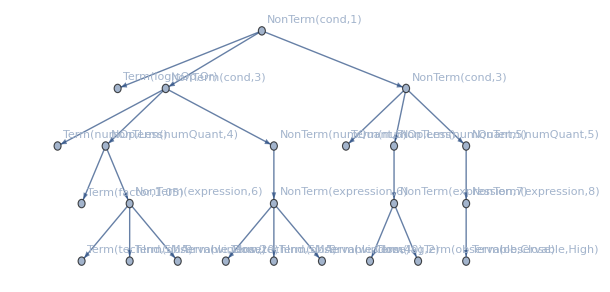

```mathematica
g2 = Graph[edgeList2,VertexLabels->labels2]
```

```mathematica
SynthesizeTree[g2,labels2,grammar]// FullForm
```

Or[Less[Times[1.05,SMA[Close,20]],SMA[Close,40]],Less[Prev[Close,2],High]]

## Operations on trees

```mathematica
Subtree[graph_,labels_,vertex_]:=Block[{children,toDelete,subtree,sublabels},
children = First@Last@Reap@DepthFirstScan[graph,vertex,{"PrevisitVertex"->(Sow[#]&)}];
toDelete = Complement[VertexList[graph],children];
subtree = VertexDelete[graph,Complement[VertexList[graph],children]];
sublabels = Cases[labels,x_/;MemberQ[children,First[x]]];

{subtree,sublabels}
];
DeleteSubtree[graph_,labels_,vertex_]:=Block[{subtree,sublabels,subVertexes,conectionRemoved,withoutSubtree,newLabels},
{subtree,sublabels} = Subtree[graph, labels, vertex];
subVertexes = VertexList[subtree];
conectionRemoved = ReplaceAll[EdgeList[graph],((x_/;!MemberQ[subVertexes,x])->(y_/;MemberQ[subVertexes,y])):>x->Empty];
withoutSubtree = If[Length[Intersection[VertexList[conectionRemoved],subVertexes]]≠ 0,
VertexDelete[conectionRemoved,subVertexes],
conectionRemoved
];
newLabels = Complement[labels,sublabels];

{Graph[withoutSubtree,VertexLabels->newLabels],newLabels}
];
InsertSubtree[graph_,labels_,subtree_,sublabels_,subtreeRoot_]:=Block[{edges,missing,missingRules,newRules,insertionRules,formattedSubtree,formattedSublabels,formattedSubtreeRoot,newTree,newLabels},
If[!MemberQ[VertexList[graph],Empty],Return[$Failed]];

edges = DeleteCases[VertexList[graph],Empty];
missing = Complement[Range[Max[edges]],edges];
missingRules = Thread[Take[VertexList[subtree],UpTo[Length[missing]]]->Take[missing,UpTo[Length[VertexList[subtree]]]]];
If[Length[VertexList[subtree]]-Length[missing]>0,
newRules = Thread[Drop[VertexList[subtree],Length[missing]]-> Range[Max[edges]+1,Max[edges]+Length[VertexList[subtree]]-Length[missing]]];
insertionRules = Join[missingRules,newRules];
,
insertionRules = missingRules;
];

formattedSubtree = EdgeList[subtree]/.insertionRules;
formattedSublabels = MapAt[ReplaceAll[#,insertionRules]&,sublabels,{All,1}];
formattedSubtreeRoot = subtreeRoot /.insertionRules;
newTree = ReplaceAll[Join[EdgeList[graph],formattedSubtree],Empty->formattedSubtreeRoot];
newLabels = SortBy[Join[labels,formattedSublabels],First];

{Graph[newTree,VertexLabels->newLabels],newLabels}
];
```

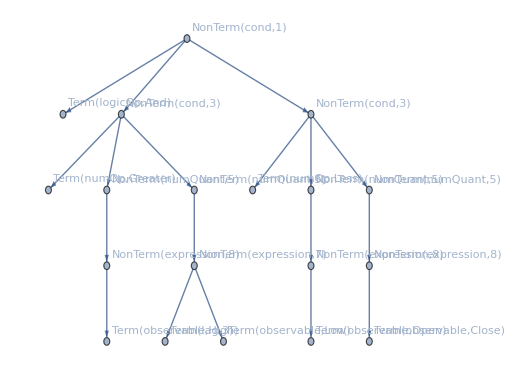

```mathematica
g1
```

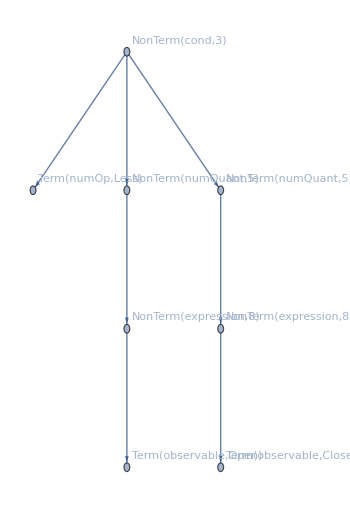
{-Graphics-,{4→NonTerm[cond,3],13→Term[numOp,Less],14→NonTerm[numQuant,5],15→NonTerm[numQuant,5],16→NonTerm[expression,8],17→Term[observable,Open],18→NonTerm[expression,8],19→Term[observable,Close]}}

```mathematica
subtree1 = Subtree[g1,labels1,4]
```

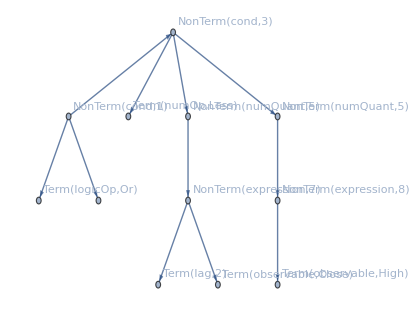
{-Graphics-,{1→NonTerm[cond,1],2→Term[logicOp,Or],4→NonTerm[cond,3],17→Term[numOp,Less],18→NonTerm[numQuant,5],19→NonTerm[numQuant,5],20→NonTerm[expression,7],21→Term[lag,2],22→Term[observable,Close],23→NonTerm[expression,8],24→Term[observable,High]}}

```mathematica
cropped2 = DeleteSubtree[g2,labels2,3]
```

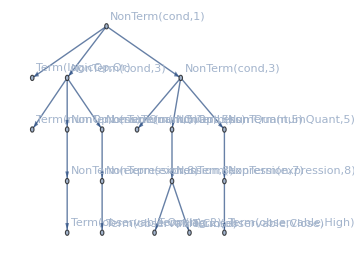
{-Graphics-,{1→NonTerm[cond,1],2→Term[logicOp,Or],3→NonTerm[cond,3],4→NonTerm[cond,3],5→Term[numOp,Less],6→NonTerm[numQuant,5],7→NonTerm[numQuant,5],8→NonTerm[expression,8],9→Term[observable,Open],10→NonTerm[expression,8],11→Term[observable,Close],17→Term[numOp,Less],18→NonTerm[numQuant,5],19→NonTerm[numQuant,5],20→NonTerm[expression,7],21→Term[lag,2],22→Term[observable,Close],23→NonTerm[expression,8],24→Term[observable,High]}}

```mathematica
inserted = InsertSubtree[First[cropped2],Last[cropped2],First[subtree1],Last[subtree1],3]
```

```mathematica
SynthesizeTree[First[inserted],Last[inserted],grammar] // FullForm
```

Or[Less[Open,Close],Less[Prev[Close,2],High]]

## Crossover

```mathematica
Crossover[graph1_,labels1_,graph2_,labels2_]:=Block[{nonterms1,nonterms2,commonNonTerms,vertex1,vertex2,cropped,sub},
nonterms1 = Cases[labels1[[All,2]],_NonTerm];
nonterms2 = Cases[labels2[[All,2]],_NonTerm];
commonNonTerms = Intersection[nonterms1,nonterms2];

vertex1 = First@RandomChoice[Drop[Position[labels1[[All,2]],Apply[Alternatives,commonNonTerms]],1]];
vertex2 = First@RandomChoice[Position[labels2[[All,2]],Last[labels1[[vertex1]]]]];
cropped = DeleteSubtree[graph1,labels1,vertex1];
sub = Subtree[graph2,labels2,vertex2];

InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub],vertex2]
];
PopulationCrossover[population_,childrenPerCouple_]:=Block[{parts},
parts = Partition[RandomSample[population],2];
Apply[Join,Table[Map[Apply[Crossover,Flatten[#,1]]&,parts],childrenPerCouple]]
];
```

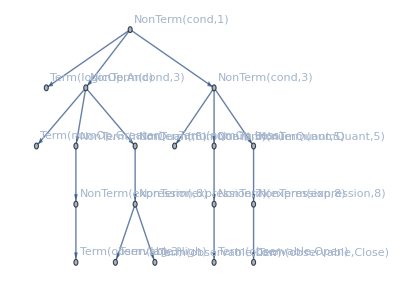
{-Graphics-,{1→NonTerm[cond,1],2→Term[logicOp,And],3→NonTerm[cond,3],4→NonTerm[cond,3],5→Term[numOp,Greater],6→NonTerm[numQuant,5],7→NonTerm[numQuant,5],8→NonTerm[expression,8],9→Term[observable,High],10→NonTerm[expression,7],11→Term[lag,3],12→Term[observable,Low],13→Term[numOp,Less],14→NonTerm[numQuant,5],15→NonTerm[numQuant,5],16→NonTerm[expression,8],17→Term[observable,Open],18→NonTerm[expression,8],19→Term[observable,Close]}}

```mathematica
{crossoverTree,crossoverLabels} = Crossover[g1,labels1,g2,labels2]
```

```mathematica
SynthesizeTree[crossoverTree,crossoverLabels,grammar]// FullForm
```

And[Greater[High,Prev[Low,3]],Less[Open,Close]]

## Mutation

```mathematica
TreeMutation[graph_,labels_]:=Crossover[graph,labels,graph,labels];
TerminalMutation[labels_,terminalSet_]:=Block[{choice,type,newTerm},
choice = RandomChoice[Cases[labels,HoldPattern[_->_Term]]];
type = First[Level[Last[choice],{1}]];
newTerm = RandomChoice[Complement[Cases[terminalSet,Term[type,_]],{Last[choice]}]];

ReplacePart[labels,First[choice]->(First[choice]->newTerm)]
];
Mutation[graph_,labels_,terminalSet_]:=Block[{mutatedSymbols},
If[RandomReal[]≥0.5,
TreeMutation[graph,labels],
mutatedSymbols = TerminalMutation[labels,terminalSet];
{Graph[EdgeList[graph],VertexLabels->mutatedSymbols],mutatedSymbols}
]
];
PopulationMutate[population_,probability_,terminalSet_,functionSet_]:=Map[If[RandomReal[]<probability,Mutation[First[#],Last[#],terminalSet,functionSet],#]&,population];
```

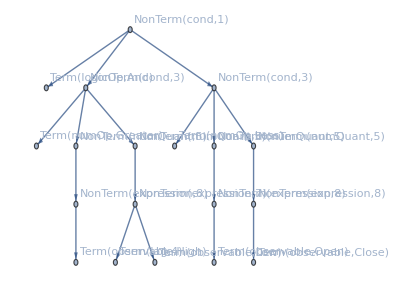
{-Graphics-,{1→NonTerm[cond,1],2→Term[logicOp,And],3→NonTerm[cond,3],4→NonTerm[cond,3],5→Term[numOp,Greater],6→NonTerm[numQuant,5],7→NonTerm[numQuant,5],8→NonTerm[expression,8],9→Term[observable,High],10→NonTerm[expression,7],11→Term[lag,4],12→Term[observable,Low],13→Term[numOp,Less],14→NonTerm[numQuant,5],15→NonTerm[numQuant,5],16→NonTerm[expression,8],17→Term[observable,Open],18→NonTerm[expression,8],19→Term[observable,Close]}}

```mathematica
{mutatedTree,mutatedLabels} = Mutation[g1,labels1,terminalSet]
```

```mathematica
SynthesizeTree[mutatedTree,mutatedLabels,grammar]
```

High>Prev[Low,4]&&Open<Close

## Fitness function

## Population initialization

## Selection

```mathematica
ProportionateSelectionIndexes[population_,n_]:=RandomSample[Reverse[Range[population]]->Range[population],n];

ProportionateRankedSelection[evaluatedGenome_,n_]:= Part[Reverse@SortBy[evaluatedGenome,Key["Score"]],ProportionateSelectionIndexes[Length[evaluatedGenome],n]];
```

## Main algorithm

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]]
```